```mathematica
q={{0.074195,0.7831},{0.077316,0.7739},{0.144645,0.6322},{0.18457,0.5609},{0.0155,0.7497},{0.01528,0.8906},{0.016587,0.8799},{0.017259,0.8745},{0.040169,0.7353},{0.015218,0.9216},{0.016171,0.9175},{0.017171,0.9159},{0.040309,0.8201},{0.074283,0.6916},{0.07781,0.682},{0.094418,0.6289},{0.074309,0.753},{0.094648,0.6975}}
```

{{0.074195,0.7831},{0.077316,0.7739},{0.144645,0.6322},{0.18457,0.5609},{0.0155,0.7497},{0.01528,0.8906},{0.016587,0.8799},{0.017259,0.8745},{0.040169,0.7353},{0.015218,0.9216},{0.016171,0.9175},{0.017171,0.9159},{0.040309,0.8201},{0.074283,0.6916},{0.07781,0.682},{0.094418,0.6289},{0.074309,0.753},{0.094648,0.6975}}

```mathematica
lm=LinearModelFit[q,{1,x,x^2},x]
```

FittedModel[0.923034-3.13065 x+6.62416 x^2]

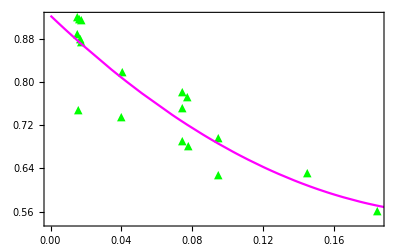

```mathematica
p1=Show[ListPlot[q,PlotStyle->Green,PlotMarkers->{"▲"}],Plot[0.9230341547832125-3.1306483061897628 x+6.624164579175652 x^2,{x,0,7},PlotStyle->{Magenta}],Frame->True]
```

```mathematica
q2={{0.074195,0.905387052965143},{0.077316,0.901798007407445},{0.144645,0.830754289792838},{0.18457,0.793677409258079},{0.0155,0.978635423845624},{0.01528,0.978932274431944},{0.016587,0.977171350437043},{0.017259,0.976268427066561},{0.040169,0.946453399167388},{0.015218,0.979015964854706},{0.016171,0.977731140461406},{0.017171,0.976386572071769},{0.040309,0.946276800624809},{0.074283,0.905285464558074},{0.07781,0.901232530686333},{0.094418,0.882625699574102},{0.074309,0.905255454164111},{0.094648,0.882373410485082}}
```

{{0.074195,0.905387},{0.077316,0.901798},{0.144645,0.830754},{0.18457,0.793677},{0.0155,0.978635},{0.01528,0.978932},{0.016587,0.977171},{0.017259,0.976268},{0.040169,0.946453},{0.015218,0.979016},{0.016171,0.977731},{0.017171,0.976387},{0.040309,0.946277},{0.074283,0.905285},{0.07781,0.901233},{0.094418,0.882626},{0.074309,0.905255},{0.094648,0.882373}}

```mathematica
lm1=LinearModelFit[q2,{1,x,x^2},x]
```

FittedModel[0.999466-1.36985 x+1.38783 x^2]

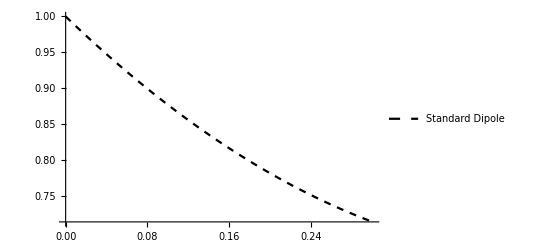

```mathematica
p2=Plot[0.9994658067123545-1.3698509783393125 x+1.387828537827042 x^2,{x,0,.3},PlotStyle->{Dashed,Black},PlotLegends->{"Standard Dipole"}]
```

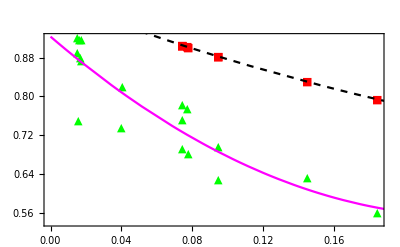

```mathematica
a=Show[p1,p2]
```

```mathematica
a= {0.074195,0.077316,0.144645,0.18457,0.0155,0.01528,0.016587,0.017259,.040169,0.015218,0.016171,0.017171,0.040309,0.074283,0.07781,0.094418,0.074309,0.094648}
```

{0.074195,0.077316,0.144645,0.18457,0.0155,0.01528,0.016587,0.017259,0.040169,0.015218,0.016171,0.017171,0.040309,0.074283,0.07781,0.094418,0.074309,0.094648}

```mathematica
b={.7831,.7739,.6322,.5609,.7497,.8906,.8799,.8745,.7353,.9216,.9175,.9159,.8201,.6916,.682,.6289,.753,.6975}
```

{0.7831,0.7739,0.6322,0.5609,0.7497,0.8906,0.8799,0.8745,0.7353,0.9216,0.9175,0.9159,0.8201,0.6916,0.682,0.6289,0.753,0.6975}

```mathematica
yerror={0.055598068831649056,0.05565946112367823,0.05988844097161335,0.06468771208062003,0.056778153289081264,0.056790741874237036,0.05671681442058604,0.05667961088802918,0.05574608076965043,0.056794300137805814,0.05674011993663505,0.056684451550889484,0.05574241080774617,0.05559962807812941,0.05567032633503662,0.05621644771550726,0.055600090674116386,0.05622645161876277}
```

{0.0555981,0.0556595,0.0598884,0.0646877,0.0567782,0.0567907,0.0567168,0.0566796,0.0557461,0.0567943,0.0567401,0.0566845,0.0557424,0.0555996,0.0556703,0.0562164,0.0556001,0.0562265}

```mathematica
plotyvalues=Table[Around[b[[i]],yerror[[i]]],{i,1,Length[b]}]
```

{0.780.06,0.770.06,0.630.06,0.560.06,0.750.06,0.890.06,0.880.06,0.870.06,0.740.06,0.920.06,0.920.06,0.920.06,0.820.06,0.690.06,0.680.06,0.630.06,0.750.06,0.700.06}

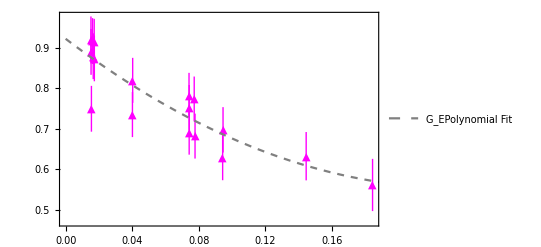

```mathematica
p3=Show[ListPlot[Transpose[{a,plotyvalues}],PlotStyle->{Magenta},PlotMarkers->{"▲"}], Plot[0.9230341547832125-3.1306483061897628 x+6.624164579175652 x^2,{x,0,.3},PlotStyle->{Dashed,Gray},PlotLegends->{"G_EPolynomial Fit"}],Frame->True]
```

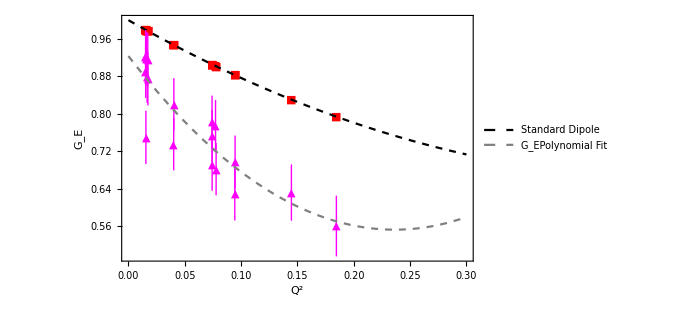

```mathematica
d=Show[p2,p3,PlotRange->All,FrameLabel->{"Q^2","G_E"},LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold},AxesStyle->Black,ImageSize->500]
```

```mathematica
Export["Dipole.png",d]
```

Dipole.png

```mathematica
q3={{0.074195,0.7831},{0.077316,0.7739},{0.144645,0.6322},{0.18457,0.5609},{0.0155,0.7497},{0.01528,0.8906},{0.016587,0.8799},{0.017259,0.8745},{0.040169,0.7353},{0.015218,0.9216},{0.016171,0.9175},{0.017171,0.9159},{0.040309,0.8201},{0.074283,0.6916},{0.07781,0.682},{0.094418,0.6289},{0.074309,0.753},{0.094648,0.6975}}
```

{{0.074195,0.7831},{0.077316,0.7739},{0.144645,0.6322},{0.18457,0.5609},{0.0155,0.7497},{0.01528,0.8906},{0.016587,0.8799},{0.017259,0.8745},{0.040169,0.7353},{0.015218,0.9216},{0.016171,0.9175},{0.017171,0.9159},{0.040309,0.8201},{0.074283,0.6916},{0.07781,0.682},{0.094418,0.6289},{0.074309,0.753},{0.094648,0.6975}}

```mathematica
model=c ^2/(c+x)^2-y
```

c^2/(c+x)^2-y

```mathematica
fit=NonlinearModelFit[q3,model,{c,y},x]
```

FittedModel[-0.0853158+0.503632/(0.70967+x)^2]

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
c | 0.70967 | 0.120868 | 5.87146 | 0.000023642
y | 0.0853158 | 0.0235458 | 3.6234 | 0.0022835

```mathematica
fit["BestFit"]
```

-0.0853158+0.503632/(0.70967+x)^2

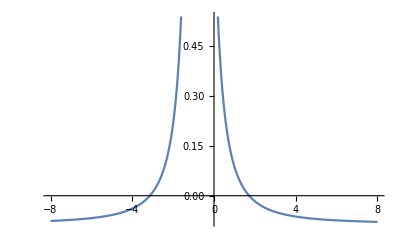

```mathematica
Plot[-0.08531582669455322+0.5036320342131383/(0.7096703701107566+x)^2,{x,-8,8}]
```

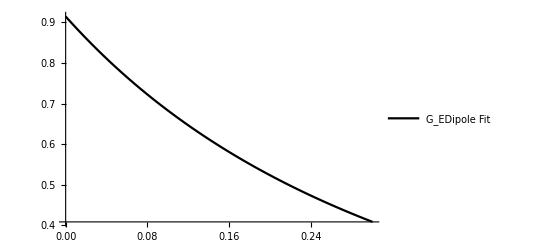

```mathematica
p1=Plot[-0.08531582669455322+0.5036320342131383/(0.7096703701107566+x)^2,{x,0,.3},PlotStyle->{Black},PlotLegends->{"G_EDipole Fit"}]
```

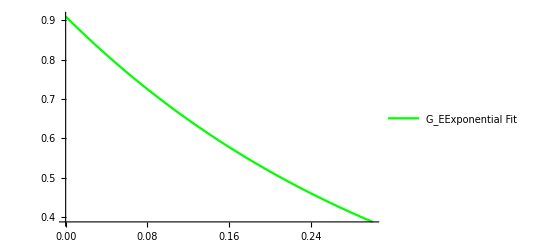

```mathematica
p4=Plot[0.9092689759118766 ⅇ^(-2.8332598305453485 t),{t,0,.3},PlotStyle->{Green},PlotLegends->{"G_EExponential Fit"}]
```

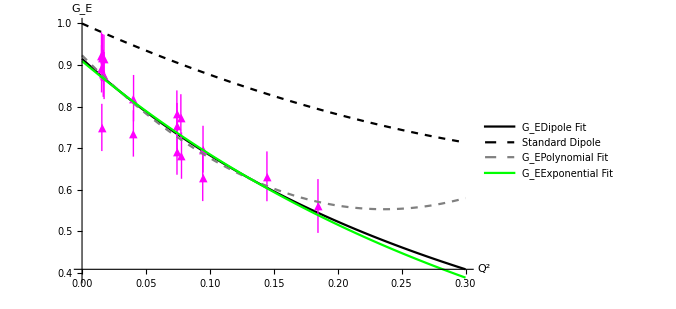

```mathematica
d=Show[p1,p2,p3,p4,  PlotRange->All,AxesLabel->{"   Q^2","G_E"},LabelStyle->{FontFamily->"Arial",14,GrayLevel[0],Bold},AxesStyle->Black,ImageSize->500]
```

```mathematica
Export["Dipole new.png",d]
```

Dipole new.png